# Omicron US analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2021-12-23

```mathematica
states=Union[seqData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Kentucky,Maryland,Massachusetts,Michigan,Minnesota,Nevada,New Jersey,New York,North Carolina,North Dakota,Ohio,Pennsylvania,Tennessee,Texas,Utah,Virginia,Washington,Washington DC,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Arizona→{{2021-12-09,124},{2021-12-10,131},{2021-12-11,76},{2021-12-12,47},{2021-12-13,144},{2021-12-14,184},{2021-12-15,96},{2021-12-16,135},{2021-12-17,129},{2021-12-18,91},{2021-12-19,45},{2021-12-20,89},{2021-12-21,69},{2021-12-22,6},{2021-12-23,0}},California→{{2021-12-09,812},{2021-12-10,770},{2021-12-11,560},{2021-12-12,213},{2021-12-13,1055},{2021-12-14,972},{2021-12-15,1321},{2021-12-16,1247},{2021-12-17,1359},{2021-12-18,1128},{2021-12-19,357},{2021-12-20,957},{2021-12-21,3169},{2021-12-22,3435},{2021-12-23,33}},Colorado→{{2021-12-09,475},{2021-12-10,392},{2021-12-11,185},{2021-12-12,271},{2021-12-13,245},{2021-12-14,373},{2021-12-15,463},{2021-12-16,422},{2021-12-17,396},{2021-12-18,248},{2021-12-19,4},{2021-12-20,42},{2021-12-21,4},{2021-12-22,19},{2021-12-23,1}},Connecticut→{{2021-12-09,144},{2021-12-10,199},{2021-12-11,113},{2021-12-12,55},{2021-12-13,161},{2021-12-14,142},{2021-12-15,138},{2021-12-16,129},{2021-12-17,138},{2021-12-18,36},{2021-12-19,29},{2021-12-20,35},{2021-12-21,43},{2021-12-22,50},{2021-12-23,1}},Florida→{{2021-12-09,188},{2021-12-10,150},{2021-12-11,102},{2021-12-12,78},{2021-12-13,114},{2021-12-14,186},{2021-12-15,229},{2021-12-16,127},{2021-12-17,119},{2021-12-18,4},{2021-12-19,8},{2021-12-20,1},{2021-12-21,7},{2021-12-22,6},{2021-12-23,0}},Georgia→{{2021-12-09,47},{2021-12-10,27},{2021-12-11,74},{2021-12-12,24},{2021-12-13,67},{2021-12-14,142},{2021-12-15,231},{2021-12-16,194},{2021-12-17,191},{2021-12-18,42},{2021-12-19,22},{2021-12-20,0},{2021-12-21,4},{2021-12-22,0},{2021-12-23,1}},Illinois→{{2021-12-09,175},{2021-12-10,205},{2021-12-11,161},{2021-12-12,130},{2021-12-13,162},{2021-12-14,309},{2021-12-15,256},{2021-12-16,215},{2021-12-17,266},{2021-12-18,10},{2021-12-19,57},{2021-12-20,2},{2021-12-21,1},{2021-12-22,4},{2021-12-23,1}},Indiana→{{2021-12-09,184},{2021-12-10,155},{2021-12-11,93},{2021-12-12,30},{2021-12-13,50},{2021-12-14,144},{2021-12-15,109},{2021-12-16,86},{2021-12-17,105},{2021-12-18,43},{2021-12-19,23},{2021-12-20,16},{2021-12-21,14},{2021-12-22,20},{2021-12-23,104}},Kentucky→{{2021-12-09,28},{2021-12-10,62},{2021-12-11,46},{2021-12-12,35},{2021-12-13,48},{2021-12-14,44},{2021-12-15,48},{2021-12-16,31},{2021-12-17,35},{2021-12-18,16},{2021-12-19,8},{2021-12-20,0},{2021-12-21,0},{2021-12-22,0},{2021-12-23,45}},Maryland→{{2021-12-09,104},{2021-12-10,104},{2021-12-11,58},{2021-12-12,56},{2021-12-13,175},{2021-12-14,305},{2021-12-15,112},{2021-12-16,110},{2021-12-17,139},{2021-12-18,39},{2021-12-19,42},{2021-12-20,30},{2021-12-21,35},{2021-12-22,27},{2021-12-23,20}},Massachusetts→{{2021-12-09,403},{2021-12-10,722},{2021-12-11,405},{2021-12-12,287},{2021-12-13,136},{2021-12-14,510},{2021-12-15,767},{2021-12-16,465},{2021-12-17,580},{2021-12-18,347},{2021-12-19,469},{2021-12-20,653},{2021-12-21,921},{2021-12-22,226},{2021-12-23,1}},Michigan→{{2021-12-09,162},{2021-12-10,135},{2021-12-11,71},{2021-12-12,29},{2021-12-13,67},{2021-12-14,127},{2021-12-15,153},{2021-12-16,95},{2021-12-17,92},{2021-12-18,9},{2021-12-19,31},{2021-12-20,0},{2021-12-21,6},{2021-12-22,23},{2021-12-23,1}},Minnesota→{{2021-12-09,555},{2021-12-10,320},{2021-12-11,170},{2021-12-12,95},{2021-12-13,219},{2021-12-14,76},{2021-12-15,42},{2021-12-16,32},{2021-12-17,60},{2021-12-18,22},{2021-12-19,86},{2021-12-20,27},{2021-12-21,0},{2021-12-22,1},{2021-12-23,2}},Nevada→{{2021-12-09,56},{2021-12-10,57},{2021-12-11,67},{2021-12-12,25},{2021-12-13,82},{2021-12-14,30},{2021-12-15,45},{2021-12-16,35},{2021-12-17,50},{2021-12-18,6},{2021-12-19,19},{2021-12-20,72},{2021-12-21,74},{2021-12-22,79},{2021-12-23,1}},New Jersey→{{2021-12-09,248},{2021-12-10,151},{2021-12-11,93},{2021-12-12,38},{2021-12-13,123},{2021-12-14,156},{2021-12-15,129},{2021-12-16,157},{2021-12-17,214},{2021-12-18,1},{2021-12-19,18},{2021-12-20,0},{2021-12-21,2},{2021-12-22,8},{2021-12-23,0}},New York→{{2021-12-09,661},{2021-12-10,495},{2021-12-11,260},{2021-12-12,222},{2021-12-13,566},{2021-12-14,543},{2021-12-15,402},{2021-12-16,381},{2021-12-17,337},{2021-12-18,94},{2021-12-19,32},{2021-12-20,63},{2021-12-21,86},{2021-12-22,45},{2021-12-23,10}},North Carolina→{{2021-12-09,136},{2021-12-10,59},{2021-12-11,61},{2021-12-12,60},{2021-12-13,180},{2021-12-14,387},{2021-12-15,108},{2021-12-16,67},{2021-12-17,98},{2021-12-18,16},{2021-12-19,28},{2021-12-20,21},{2021-12-21,1},{2021-12-22,1},{2021-12-23,1}},North Dakota→{{2021-12-09,44},{2021-12-10,55},{2021-12-11,29},{2021-12-12,36},{2021-12-13,127},{2021-12-14,78},{2021-12-15,54},{2021-12-16,18},{2021-12-17,59},{2021-12-18,17},{2021-12-19,28},{2021-12-20,37},{2021-12-21,92},{2021-12-22,54},{2021-12-23,106}},Ohio→{{2021-12-09,229},{2021-12-10,226},{2021-12-11,78},{2021-12-12,55},{2021-12-13,152},{2021-12-14,236},{2021-12-15,148},{2021-12-16,155},{2021-12-17,239},{2021-12-18,21},{2021-12-19,33},{2021-12-20,88},{2021-12-21,22},{2021-12-22,19},{2021-12-23,13}},Pennsylvania→{{2021-12-09,231},{2021-12-10,135},{2021-12-11,60},{2021-12-12,12},{2021-12-13,43},{2021-12-14,125},{2021-12-15,140},{2021-12-16,118},{2021-12-17,110},{2021-12-18,26},{2021-12-19,3},{2021-12-20,0},{2021-12-21,0},{2021-12-22,0},{2021-12-23,0}},Tennessee→{{2021-12-09,71},{2021-12-10,51},{2021-12-11,44},{2021-12-12,28},{2021-12-13,31},{2021-12-14,67},{2021-12-15,76},{2021-12-16,29},{2021-12-17,40},{2021-12-18,4},{2021-12-19,29},{2021-12-20,0},{2021-12-21,7},{2021-12-22,7},{2021-12-23,0}},Texas→{{2021-12-09,166},{2021-12-10,196},{2021-12-11,211},{2021-12-12,110},{2021-12-13,242},{2021-12-14,415},{2021-12-15,470},{2021-12-16,282},{2021-12-17,353},{2021-12-18,158},{2021-12-19,59},{2021-12-20,96},{2021-12-21,39},{2021-12-22,355},{2021-12-23,10}},Utah→{{2021-12-09,92},{2021-12-10,73},{2021-12-11,65},{2021-12-12,65},{2021-12-13,92},{2021-12-14,143},{2021-12-15,65},{2021-12-16,17},{2021-12-17,49},{2021-12-18,26},{2021-12-19,45},{2021-12-20,73},{2021-12-21,88},{2021-12-22,91},{2021-12-23,47}},Virginia→{{2021-12-09,87},{2021-12-10,23},{2021-12-11,8},{2021-12-12,10},{2021-12-13,100},{2021-12-14,150},{2021-12-15,47},{2021-12-16,26},{2021-12-17,16},{2021-12-18,1},{2021-12-19,4},{2021-12-20,2},{2021-12-21,1},{2021-12-22,3},{2021-12-23,1}},Washington→{{2021-12-09,274},{2021-12-10,373},{2021-12-11,250},{2021-12-12,83},{2021-12-13,280},{2021-12-14,315},{2021-12-15,203},{2021-12-16,238},{2021-12-17,174},{2021-12-18,77},{2021-12-19,22},{2021-12-20,24},{2021-12-21,34},{2021-12-22,41},{2021-12-23,5}},Washington DC→{{2021-12-09,34},{2021-12-10,38},{2021-12-11,36},{2021-12-12,18},{2021-12-13,32},{2021-12-14,92},{2021-12-15,60},{2021-12-16,77},{2021-12-17,52},{2021-12-18,0},{2021-12-19,2},{2021-12-20,0},{2021-12-21,1},{2021-12-22,0},{2021-12-23,0}},Wisconsin→{{2021-12-09,213},{2021-12-10,181},{2021-12-11,101},{2021-12-12,96},{2021-12-13,201},{2021-12-14,263},{2021-12-15,294},{2021-12-16,228},{2021-12-17,246},{2021-12-18,56},{2021-12-19,33},{2021-12-20,110},{2021-12-21,72},{2021-12-22,77},{2021-12-23,37}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

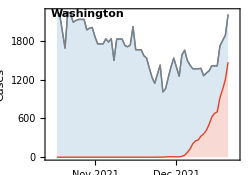

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

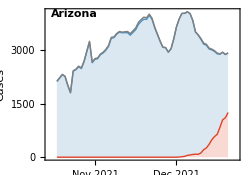
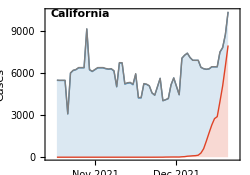
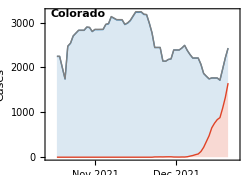
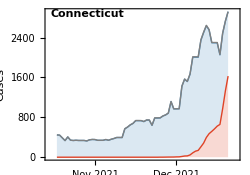
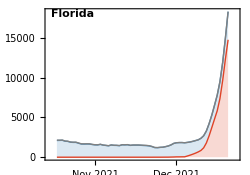
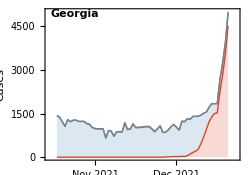
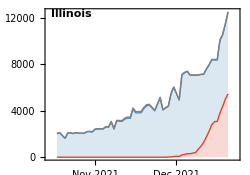
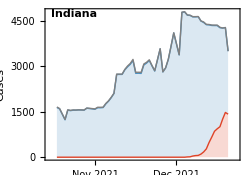
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=20000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-02

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

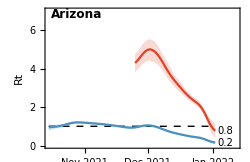
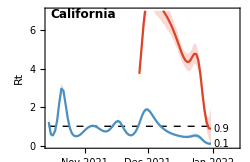
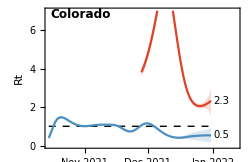
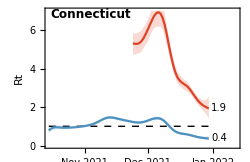
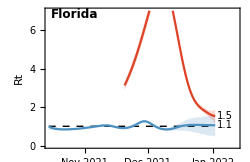
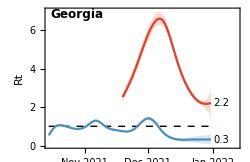
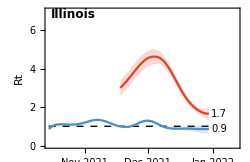
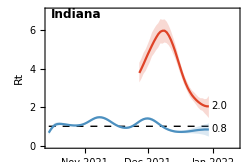
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arizona→{2022-01-02,0.8,0.4,1.2},California→{2021-12-31,0.9,0.1,1.9},Colorado→{2021-12-31,2.3,1.5,3.},Connecticut→{2021-12-30,1.9,1.4,2.5},Florida→{2022-01-02,1.5,1.1,1.9},Georgia→{2021-12-31,2.2,1.4,2.9},Illinois→{2021-12-30,1.7,1.3,2.},Indiana→{2021-12-30,2.,1.4,2.6},Kentucky→{2021-12-29,2.9,2.5,3.3},Maryland→{2022-01-02,2.,1.7,2.3},Massachusetts→{2021-12-31,2.4,2.,2.8},Michigan→{2021-12-29,2.1,1.1,3.},Minnesota→{2021-12-30,3.2,2.4,4.},Nevada→{2021-12-30,3.,2.4,3.7},New Jersey→{2022-01-02,1.9,1.5,2.2},New York→{2022-01-02,1.5,1.1,1.9},North Carolina→{2021-12-31,13.8,7.7,20.},North Dakota→{2022-01-02,2.3,2.,2.5},Ohio→{2022-01-02,2.7,2.2,3.2},Pennsylvania→{2022-01-02,2.4,2.1,2.7},Tennessee→{2021-12-30,2.9,2.6,3.2},Texas→{2021-12-30,0.4,0.1,0.7},Utah→{2021-12-30,3.,2.6,3.5},Virginia→{2021-12-31,2.6,2.3,2.9},Washington→{2021-12-30,0.8,0.3,1.2},Washington DC→{2021-12-30,0.5,0.3,0.8},Wisconsin→{2021-12-31,1.9,1.3,2.5}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rData=DeleteCases[rData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,15]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arizona→{2022-01-02,-0.04,-0.15,0.03},California→{2021-12-31,-0.02,-0.4,0.11},Colorado→{2021-12-31,0.14,0.07,0.18},Connecticut→{2021-12-30,0.11,0.06,0.16},Florida→{2022-01-02,0.07,0.02,0.1},Georgia→{2021-12-31,0.13,0.06,0.18},Illinois→{2021-12-30,0.08,0.05,0.12},Indiana→{2021-12-30,0.12,0.06,0.16},Kentucky→{2021-12-29,0.18,0.15,0.2},Maryland→{2022-01-02,0.12,0.09,0.14},Massachusetts→{2021-12-31,0.15,0.11,0.18},Michigan→{2021-12-29,0.13,0.02,0.18},Minnesota→{2021-12-30,0.2,0.15,0.24},Nevada→{2021-12-30,0.19,0.15,0.22},New Jersey→{2022-01-02,0.11,0.07,0.14},New York→{2022-01-02,0.06,0.02,0.1},North Carolina→{2021-12-31,0.47,0.36,0.55},North Dakota→{2022-01-02,0.14,0.12,0.16},Ohio→{2022-01-02,0.17,0.13,0.2},Pennsylvania→{2022-01-02,0.15,0.12,0.17},Tennessee→{2021-12-30,0.18,0.16,0.2},Texas→{2021-12-30,-0.14,-0.31,-0.06},Utah→{2021-12-30,0.19,0.16,0.21},Virginia→{2021-12-31,0.16,0.14,0.18},Washington→{2021-12-30,-0.04,-0.17,0.03},Washington DC→{2021-12-30,-0.1,-0.17,-0.04},Wisconsin→{2021-12-31,0.1,0.04,0.15}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arizona→{2022-01-02,-16.3,27.6,-4.8},California→{2021-12-31,-30.2,6.3,-1.7},Colorado→{2021-12-31,4.9,3.8,9.7},Connecticut→{2021-12-30,6.3,4.4,12.2},Florida→{2022-01-02,9.9,6.6,32.},Georgia→{2021-12-31,5.2,3.9,11.4},Illinois→{2021-12-30,8.3,5.9,15.4},Indiana→{2021-12-30,5.8,4.4,11.8},Kentucky→{2021-12-29,3.8,3.4,4.5},Maryland→{2022-01-02,5.8,4.9,8.1},Massachusetts→{2021-12-31,4.7,3.9,6.2},Michigan→{2021-12-29,5.5,3.8,45.3},Minnesota→{2021-12-30,3.5,2.9,4.6},Nevada→{2021-12-30,3.7,3.1,4.7},New Jersey→{2022-01-02,6.5,5.1,9.6},New York→{2022-01-02,10.7,6.7,32.1},North Carolina→{2021-12-31,1.5,1.3,1.9},North Dakota→{2022-01-02,5.1,4.4,5.9},Ohio→{2022-01-02,4.2,3.5,5.4},Pennsylvania→{2022-01-02,4.7,4.1,5.6},Tennessee→{2021-12-30,3.9,3.5,4.4},Texas→{2021-12-30,-5.1,-12.,-2.3},Utah→{2021-12-30,3.7,3.2,4.4},Virginia→{2021-12-31,4.4,3.9,5.},Washington→{2021-12-30,-18.4,21.1,-4.2},Washington DC→{2021-12-30,-7.1,-16.8,-4.1},Wisconsin→{2021-12-31,6.7,4.5,17.4}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{20,240000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,states]
```

{Arizona→{2022-01-02,4281,3064,5486},California→{2021-12-31,58072,20158,97229},Colorado→{2021-12-31,10947,8118,13455},Connecticut→{2021-12-30,8368,6534,10116},Florida→{2022-01-02,70970,50175,92702},Georgia→{2021-12-31,27649,18645,36055},Illinois→{2021-12-30,20566,12228,27911},Indiana→{2021-12-30,10410,5788,15115},Kentucky→{2021-12-29,2355,1704,3023},Maryland→{2022-01-02,18611,12920,24180},Massachusetts→{2021-12-31,23725,18887,28263},Michigan→{2021-12-29,15218,11330,19021},Minnesota→{2021-12-30,4654,3658,5488},Nevada→{2021-12-30,2293,1634,2864},New Jersey→{2022-01-02,30423,22816,37778},New York→{2022-01-02,61190,51781,71530},North Carolina→{2021-12-31,15460,13297,17668},North Dakota→{2022-01-02,460,358,572},Ohio→{2022-01-02,31588,24512,38151},Pennsylvania→{2022-01-02,20479,17594,23278},Tennessee→{2021-12-30,10286,8031,12983},Texas→{2021-12-30,13126,7477,18623},Utah→{2021-12-30,4072,3015,5025},Virginia→{2021-12-31,15399,11640,18641},Washington→{2021-12-30,5504,4115,6874},Washington DC→{2021-12-30,3464,2273,4658},Wisconsin→{2021-12-31,7548,5753,9349}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[state_,variant_]:=Module[{popSize,stateName},
stateName=StringReplace[state," "->""];
popSize=QuantityMagnitude[AdministrativeDivisionData[{stateName, "UnitedStates"},"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[state,variant]]
]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsDelta,pairsOmicron},
pairsDelta=phaseGather[country,"Delta"];
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsDelta,{Last[pairsDelta]},pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,150},
{-0.25,0.45}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[2]],colors[[2]],colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,states];
```

```mathematica
fig=Grid[gappedPartition[panels,4],Spacings->{1,1},Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt.png

```mathematica
stateLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,states];
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,150},
{-0.1,0.35}},PlotStyle->Directive[colors[[3]],Opacity[0.5]]];
```

```mathematica
statePoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,states];
```

```mathematica
figPoints=ListLogLinearPlot[statePoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,150},
{-0.1,0.35}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

```mathematica
stateLines=Map[With[{pairs=phaseGather[#,"Delta"]},pairs]&,states];
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,150},
{-0.1,0.35}},PlotStyle->Directive[colors[[2]],Opacity[0.5]]];
```

```mathematica
statePoints=Map[With[{pairs=phaseGather[#,"Delta"]},Last[pairs]]&,states];
```

```mathematica
figPoints=ListLogLinearPlot[statePoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,150},
{-0.1,0.35}},PlotStyle->Directive[colors[[2]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-